## Analisis y simulación de un mecanismo de corredera

## Datos iniciales del mecanismo

```mathematica
AB=10;CE=30;AE=90;
α2=5;ω20=2;θ20=π/2;
θ4=π/3
```

π/3

```mathematica
eqd1=θ2''[t]==α2
```

θ2''[t]==5

```mathematica
sol=DSolve[{eqd1,θ2[0]==θ20,θ2'[0]==ω20},θ2[t],t]//Expand
```

{{θ2[t]→π/2+2 t+(5 t^2)/2}}

```mathematica
θ2=θ2[t] /. sol[[1]]
```

π/2+2 t+(5 t^2)/2

```mathematica
ω2=D[θ2,t]
```

2+5 t

## Determinacion de la variacion de las posiciones

```mathematica
R1=d;
R2=a ⅇ^(ⅈ θ2);
R3=b ⅇ^(ⅈ θ3);
R4=c ⅇ^(ⅈ θ4);
```

Se define la ecuacion de cierre de forma polar a trigonometrica

```mathematica
eqcierre=(R2+R3-R1-R4//ExpToTrig//Expand)==0
```

-c/2-1/2 ⅈ √3 c-d+ⅈ a Cos[2 t+(5 t^2)/2]+b Cos[θ3]-a Sin[2 t+(5 t^2)/2]+ⅈ b Sin[θ3]==0

Se descompone en 2 ecuaciones, una para la parte real otra para la parte imaginaria

```mathematica
ecReal=-a Cos[θ2]+c Cos[θ4]+d==b Cos[θ3]
```

c/2+d+a Sin[2 t+(5 t^2)/2]==b Cos[θ3]

```mathematica
ecImag=-a Sin[θ2]+c Sin[θ4]==b Sin[θ3]
```

(√3 c)/2-a Cos[2 t+(5 t^2)/2]==b Sin[θ3]

Se acomoda para luego elevar al cuadrado ambas eq, sumarlas y de esta forma “eliminarnos” la parte q involucra θ3

```mathematica
ecS2=ecReal[[1]]^2+ecImag[[1]]^2==ecReal[[2]]^2+ecImag[[2]]^2//Expand//Simplify
```

a^2+c^2+c d+d^2+a (c+2 d) Sin[1/2 t (4+5 t)]==b^2+√3 a c Cos[1/2 t (4+5 t)]

Ahora se resuelve para obtener la magnitud de R4, esto es c

```mathematica
solR4=Solve[ecS2,c]
```

{{c→1/2 (-d+√3 a Cos[1/2 t (4+5 t)]-a Sin[1/2 t (4+5 t)]-√((d-√3 a Cos[1/2 t (4+5 t)]+a Sin[1/2 t (4+5 t)])^2-4 (a^2-b^2+d^2+2 a d Sin[1/2 t (4+5 t)])))},{c→1/2 (-d+√3 a Cos[1/2 t (4+5 t)]-a Sin[1/2 t (4+5 t)]+√((d-√3 a Cos[1/2 t (4+5 t)]+a Sin[1/2 t (4+5 t)])^2-4 (a^2-b^2+d^2+2 a d Sin[1/2 t (4+5 t)])))}}

Resta entonces determinar θ3, para ello vuelvo al sistema de ecuaciones

```mathematica
solθ3=Solve[ecReal,θ3]
```

{{θ3→ConditionalExpression[-ArcCos[(c+2 d+2 a Sin[2 t+(5 t^2)/2])/(2 b)]+2 π C[1], C[1]∈ℤ]},{θ3→ConditionalExpression[ArcCos[(c+2 d+2 a Sin[2 t+(5 t^2)/2])/(2 b)]+2 π C[1], C[1]∈ℤ]}}

Redefino los fasores con la magnitud de R4 y la expresion de θ3

```mathematica
AB=10; a=10;
AE=90;
CE=30;
BC=√(AE^2+(CE-AB)^2); b=BC;
AD=AE-CE/Tan[θ4]; d=AD;
c=1/2 (-d+√3 a Cos[1/2 t (4+5 t)]-a Sin[1/2 t (4+5 t)]+√((d-√3 a Cos[1/2 t (4+5 t)]+a Sin[1/2 t (4+5 t)])^2-4 (a^2-b^2+d^2+2 a d Sin[1/2 t (4+5 t)])));
θ3=ArcCos[(c+2 d+2 a Sin[2 t+(5 t^2)/2])/(2 b)];
```

```mathematica
R1=d;
R2=a ⅇ^(ⅈ θ2);
R3=b ⅇ^(ⅈ θ3);
R4=c ⅇ^(ⅈ θ4);
```

Se crea un intervalo de tiempo arbitrario y las tablas de posiciones para los puntos de interes, B y C

```mathematica
T0=10; Nframe=200;
PBi=Table[{Re[R2],Im[R2]}/.t->i1//N,{i1,0,T0,T0/Nframe}];
PCi=Table[{Re[R1+R4],Im[R1+R4]}/.t->i1//N,{i1,0,T0,T0/Nframe}];
```

Para “estetizar” el plot y diferenciar los puntos de interes, se define tanto el punto B y C en su posicion inicial, ademas de los puntos fijos A y E.

```mathematica
Bx0=Re[R2]/.t->0//N;
By0=Im[R2]/.t->0//N;
Cx0=Re[R2+R3]/.t->0//N;
Cy0=Im[R2+R3]/.t->0//N;
Ax=0;
Ay=0;
Ex=90;
Ey=0;
```

Se definen las graficas corresondientes a los puntos, lineas (barras) e indicaciones

```mathematica
BB=Point[{Bx0,By0}];
CC=Point[{{Cx0,Cy0}}];
AA=Point[{Ax,Ay}];
EE=Point[{Ex,Ey}];
LR2=Line[{{Ax,Ay},{Bx0,By0}}];
LR3=Line[{{Bx0,By0},{Cx0,Cy0}}];
LR1=Line[{{Ax,Ay},{Ex,Ey}}];
LR4=Line[{{Ex,Ey},{Cx0,Cy0}}];
LRR=Line[{{Ax,Ay},{Cx0,Cy0}}];
BText=Text[Style["B",Bold],{Bx0-3,By0+3}];
CText=Text[Style["C",Bold],{Cx0-3,Cy0+3}];
AText=Text[Style["A",Bold],{Ax+3,Ay-3}];
EText=Text[Style["E",Bold],{Ex+3,Ey+3}];
```

```mathematica
graphline=Graphics[{{Red,Thick,LR2},{Red,Thick,LR3},{Red,Thick,LR1},{Red,Thick,LR4},{Red,Dashed,LRR}},AspectRatio->1,PlotRange->{{-20,110},{-20,40}}];
graphpoint=Graphics[{{PointSize[Medium],BB},{PointSize[Medium],CC},{PointSize[Medium],AA},{PointSize[Medium],EE}},AspectRatio->1,PlotRange->{{-20,110},{-20,40}}];
graphtxt=Graphics[{AText,BText,CText,EText},AspectRatio->1,PlotRange->{{-20,110},{-20,40}}];
```

```mathematica
g1=ListPlot[PBi,PlotStyle->Blue];
g2=ListPlot[PCi,PlotStyle->Blue];
```

Se plotean en simultaneo trayectorias, lineas (barras), puntos e indicaciones

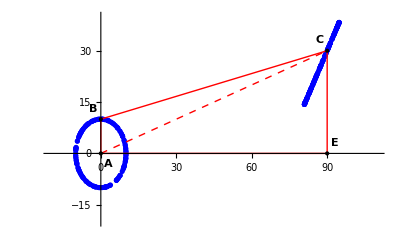

```mathematica
Framed[Show[g1,g2,graphline,graphtxt,graphpoint,PlotRange->{{-20,110},{-20,40}}]]
```

A modo ilustrativo se realizara lo mismo para un valor de t=13s

```mathematica
Bxt=Re[R2]/.t->13//N;
Byt=Im[R2]/.t->13//N;
Cxt=Re[R2+R3]/.t->13//N;
Cyt=Im[R2+R3]/.t->13//N;
```

```mathematica
BBt=Point[{Bxt,Byt}];
CCt=Point[{{Cxt,Cyt}}];
LR2t=Line[{{Ax,Ay},{Bxt,Byt}}];
LR3t=Line[{{Bxt,Byt},{Cxt,Cyt}}];
LR1t=Line[{{Ax,Ay},{Ex,Ey}}];
LR4t=Line[{{Ex,Ey},{Cxt,Cyt}}];
LRRt=Line[{{Ax,Ay},{Cxt,Cyt}}];
BTextt=Text[Style["B",Bold],{Bxt-3,Byt+3}];
CTextt=Text[Style["C",Bold],{Cxt-3,Cyt+3}];
ATextt=Text[Style["A",Bold],{Ax+3,Ay-3}];
ETextt=Text[Style["E",Bold],{Ex+3,Ey+3}];
```

```mathematica
graphlinet=Graphics[{{Red,Thick,LR2t},{Red,Thick,LR3t},{Red,Thick,LR1t},{Red,Thick,LR4t},{Red,Dashed,LRRt}},AspectRatio->1,PlotRange->{{-20,110},{-20,40}}];
graphpointt=Graphics[{{PointSize[Medium],BBt},{PointSize[Medium],CCt},{PointSize[Medium],AA},{PointSize[Medium],EE}},AspectRatio->1,PlotRange->{{-20,110},{-20,40}}];
```

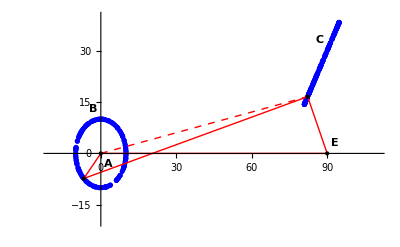

```mathematica
Framed[Show[g1,g2,graphlinet,graphtxt,graphpointt,PlotRange->{{-20,110},{-20,40}}]]
```

La animacion del mecanismo de 4 barras

```mathematica
animacion=Animate[Framed[Graphics[{{Red,Thick,Line[{{Ax,Ay},PBi[[i]]}]},{Red,Thick,Line[{PBi[[i]],PCi[[i]]}]},{Red,Thick,Line[{PCi[[i]],{Ex,Ey}}]},{Dashed,Blue,Line[{PCi[[22]],PCi[[11]]}]},{PointSize[Medium],Point[PBi[[i]]]},{PointSize[Medium],Point[PCi[[i]]]},{PointSize[Medium],Point[{Ax,Ay}]},{PointSize[Medium],Point[{Ex,Ey}]},EText,AText,Text[Style["B",Bold],PBi[[i]]+{-3,3}],Text[Style["C",Bold],PCi[[i]]+{-3,3}],{Dashed,Blue,Circle[{0,0},10]}},PlotRange->{{-20,110},{-20,40}},Axes->True]],{i,1,50,1,AnimationRunning->False,AnimationRate->3}]
```

```mathematica
Export["C:\\Users\\nfrat\\OneDrive\\Escritorio\\Materias\\4to Año\\Elementos de Maquina\\animacion2.mp4",animacion,"AnimationDuration"->20,"FrameRate"->24]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

C:\Users\nfrat\OneDrive\Escritorio\Materias\4to Año\Elementos de Maquina\animacion2.mp4

Se puede observar que la manivela del mecanismo (i.e segmento AB) rota 360°, lo cual se puede comprobar matematicamente por el criterio de Grashof-Gruebler

|L_l|+|L_s|<=|L_p|+|L_q|

donde:

L_l->longitud eslabon mas largo (BC) 
L_s->longitud eslabon mas corto (AB)
L_p,L_p->longitud eslabones restantes (CE,AE)

```mathematica
BC+AB<=CE+AE
```

True

## Determinacion de la velocidad y aceleracion

```mathematica
vR1=D[R1,t];
vR2=D[R2,t];
vR3=D[R3,t];
vR4=D[R4,t];
```

```mathematica
aR1=D[R1,t,t];
aR2=D[R2,t,t];
aR3=D[R3,t,t];
aR4=D[R4,t,t];
```

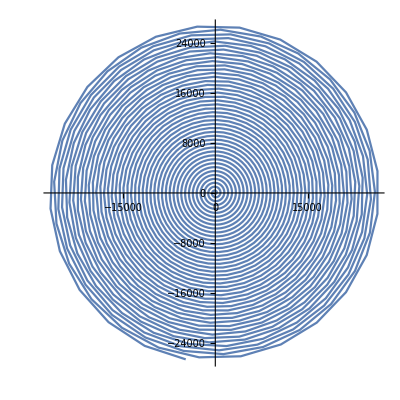

```mathematica
ListLinePlot[Table[{Re[aR2],Im[aR2]}/.t->i1//N,{i1,0,T0,T0/2000}],AspectRatio->1]
```

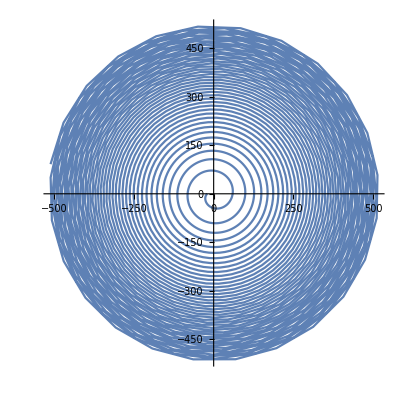

```mathematica
ListLinePlot[Table[{Re[vR2],Im[vR2]}/.t->i1//N,{i1,0,T0,T0/2000}],AspectRatio->1]
```

```mathematica
ListLinePlot3D[Table[{Re[vR2+vR3],Im[vR2+vR3],i1}/.t->i1//N,{i1,0,T0,T0/1000}],AxesLabel->{Style["x",Bold,Black,Medium],Style["y",Bold,Black,Medium],Style["t",Bold,Black,Medium]},AspectRatio->1]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Table[{Re[vR2],Im[vR2],i1}/.t->i1//N,{i1,0,T0,T0/2000}],AxesLabel->{Style["x",Bold,Black,Medium],Style["y",Bold,Black,Medium],Style["t",Bold,Black,Medium]},AspectRatio->1]
```

-Graphics3D-

```mathematica
vr2anim=Table[{Re[vR2],Im[vR2],i1}/.t->i1//N,{i1,0,T0,T0/2000}];
```

```mathematica
Animate[ListLinePlot3D[Take[vr2anim,i],AxesLabel->{Style["x",Bold,Black,Medium],Style["y",Bold,Black,Medium],Style["t",Bold,Black,Medium]},AspectRatio->1],{i,1,1500,2,AnimationRunning->False,AnimationRate->50}]
```

```mathematica
vr3anim=Table[{Re[vR2+vR3],Im[vR2+vR3],i1}/.t->i1//N,{i1,0,T0,T0/2000}];
```

```mathematica
Animate[ListLinePlot3D[Take[vr3anim,i],AxesLabel->{Style["x",Bold,Black,Medium],Style["y",Bold,Black,Medium],Style["t",Bold,Black,Medium]},AspectRatio->1],{i,1,1500,2,AnimationRunning->False,AnimationRate->50}]
```